# P-Value Hacking

Suppose we generate possible correlation coefficients in this way.
We have it between variables.
The variables follow a standard normal distribution.
There are 18 pairs of variables.
The correlation calculation is done 10000 times.
Notice that the correlation coefficient can easily exceed 0.5.

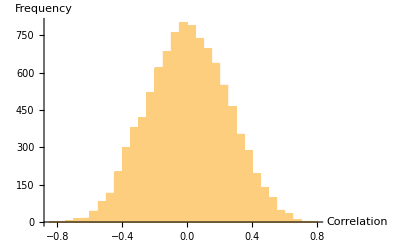

```mathematica
Histogram[Table[a = RandomVariate[NormalDistribution[],18];
b = RandomVariate[NormalDistribution[],18]; Correlation[a,b],{10000}], AxesLabel->{"Correlation","Frequency"}]
```

Compare this to a similarly fat tailed random variable.
We get the normal distribution for the distribution.
Generate the p-value for 20 variables.

```mathematica
dist1=NormalDistribution[0.3,1];
ta = Table[ran=RandomVariate[dist1,20];
SurvivalFunction[StudentTDistribution[20], Mean[ran]/(StandardDeviation[ran]/Sqrt[20])],{10^4}];
(* Not very sure about this. *)
```

We can determine the mean of the table.

```mathematica
Mean[ta] (*Most options are below the p-value 0.05*)
```

0.175591

```mathematica
?Quantile
```

We can see the various quantiles for various p-values.

```mathematica
Quantile[ta,0.36590] // N
```

0.0499641

```mathematica
Quantile[ta,0.025] // N
```

0.000794859

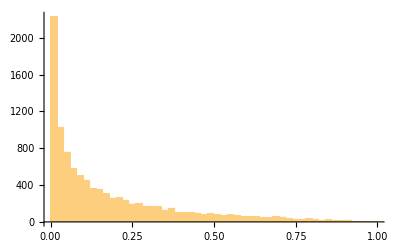

```mathematica
Histogram[ta,60]
```

```mathematica
CDF[EmpiricalDistribution[ta], 0.01]
```

0.1457